```mathematica
Nuklearna fizika
```

```mathematica
Radioaktivno sočivo - Super Takumar 55mm
```

```mathematica
ClearAll["Global`*"]
sviPodaci=Import["D:\\Fizika\\FTN Cacak\\RMFP\\2021-22\\14. Nuklearna fizika\\Radioaktivno socivo.xlsx"];
plot1=ListPlot[{sviPodaci[[1,All,{1,2}]]},
PlotStyle->Red,
PlotMarkers->{"◆"},
PlotLabel->Style["Broj otkucaja svakih 10s",Black,Italic],
Filling->Axis,
PlotRange->{{0,1250},{0,300}},
AxesLabel->{"Vreme (s)","Broj otkucaja"},
AxesOrigin->{0,0},
ImageSize->{850,Automatic}];
Manipulate[LocatorPane[Dynamic[sviPodaci],Show[plot1,Epilog->{Red,PointSize[Large],Point[Dynamic[sviPodaci]]}]],{{sviPodaci,{1000,200}}}]
```

Show::gtype: Symbol is not a type of graphics.

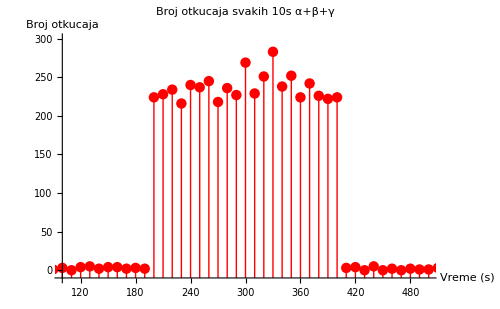

```mathematica
sviPodaci=Import["D:\\Fizika\\FTN Cacak\\RMFP\\2021-22\\14. Nuklearna fizika\\Radioaktivno socivo.xlsx"];
ListPlot[{sviPodaci[[1,All,{1,2}]]},
PlotStyle->{Red,PointSize[0.015]},
PlotLabel->Style["Broj otkucaja svakih 10s
α+β+γ",Black,Italic],
Filling->Axis,
FillingStyle->Red,
PlotRange->{{100,500},{-10,300}},
AxesLabel->{"Vreme (s)","Broj otkucaja"},
AxesOrigin->{100,-10},
ImageSize->{500,Automatic}]
```

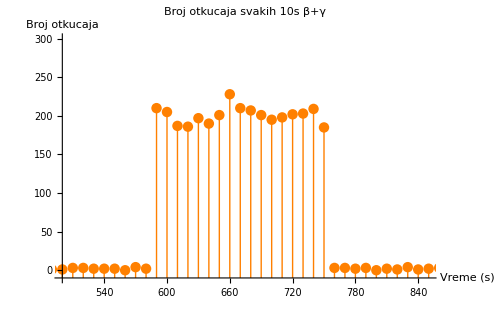

```mathematica
sviPodaci=Import["D:\\Fizika\\FTN Cacak\\RMFP\\2021-22\\14. Nuklearna fizika\\Radioaktivno socivo.xlsx"];
ListPlot[{sviPodaci[[1,All,{1,2}]]},
PlotStyle->{Orange,PointSize[0.015]},
PlotLabel->Style["Broj otkucaja svakih 10s
β+γ",Black,Italic],
Filling->Axis,
FillingStyle->Orange,
PlotRange->{{500,850},{-10,300}},
AxesLabel->{"Vreme (s)","Broj otkucaja"},
AxesOrigin->{500,-10},
ImageSize->{500,Automatic}]
```

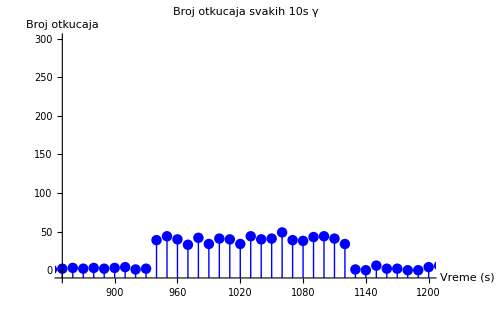

```mathematica
sviPodaci=Import["D:\\Fizika\\FTN Cacak\\RMFP\\2021-22\\14. Nuklearna fizika\\Radioaktivno socivo.xlsx"];
ListPlot[{sviPodaci[[1,All,{1,2}]]},
PlotStyle->{Blue,PointSize[0.015]},
PlotLabel->Style["Broj otkucaja svakih 10s
γ",Black,Italic],
Filling->Axis,
FillingStyle->Blue,
PlotRange->{{850,1200},{-10,300}},
AxesLabel->{"Vreme (s)","Broj otkucaja"},
AxesOrigin->{850,-10},
ImageSize->{500,Automatic}]
```

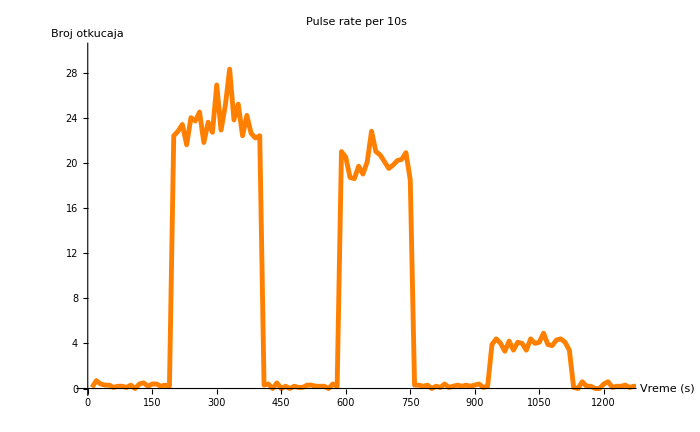

```mathematica
sviPodaci=Import["D:\\Fizika\\FTN Cacak\\RMFP\\2021-22\\14. Nuklearna fizika\\Radioaktivno socivo.xlsx"];
ListLinePlot[{sviPodaci[[1,All,{1,3}]]},
PlotStyle->{Orange, Thickness[0.005]},
PlotLabel->Style["Pulse rate per 10s",Black,Italic],
PlotRange->{{0,1250},{0,30}},
AxesLabel->{"Vreme (s)","Broj otkucaja"},
AxesOrigin->{0,0},
ImageSize->{700,Automatic}]
```

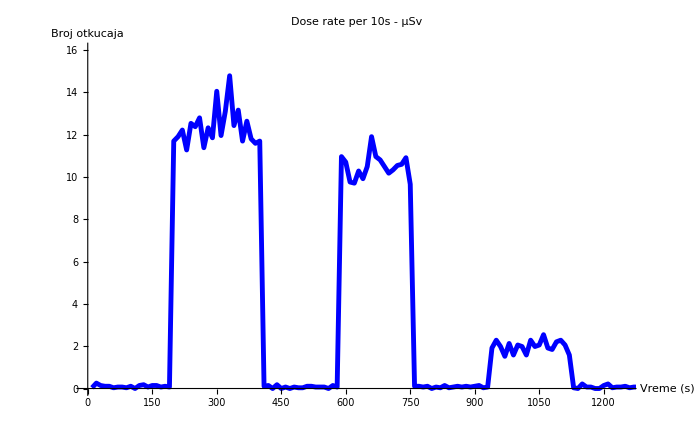

```mathematica
sviPodaci=Import["D:\\Fizika\\FTN Cacak\\RMFP\\2021-22\\14. Nuklearna fizika\\Radioaktivno socivo.xlsx"];
ListLinePlot[{sviPodaci[[1,All,{1,4}]]},
PlotStyle->{Blue, Thickness[0.005]},
PlotLabel->Style["Dose rate per 10s - μSv",Black,Italic],
PlotRange->{{0,1250},{0,16}},
AxesLabel->{"Vreme (s)","Broj otkucaja"},
AxesOrigin->{0,0},
ImageSize->{700,Automatic}]
```

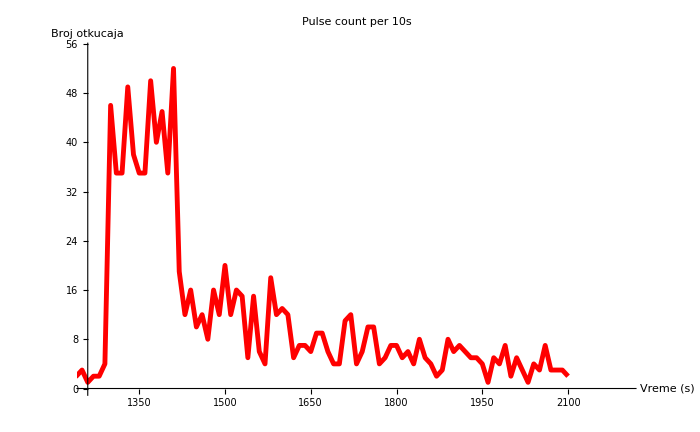

```mathematica
sviPodaci=Import["D:\\Fizika\\FTN Cacak\\RMFP\\2021-22\\14. Nuklearna fizika\\Radioaktivno socivo.xlsx"];
ListLinePlot[{sviPodaci[[1,All,{1,2}]]},
PlotStyle->{Red,Thickness[0.005]},
PlotLabel->Style["Pulse count per 10s",Black,Italic],
PlotRange->{{1260,2200},{0,55}},
AxesLabel->{"Vreme (s)","Broj otkucaja"},
AxesOrigin->{1260,0},
ImageSize->{700,Automatic}]
```

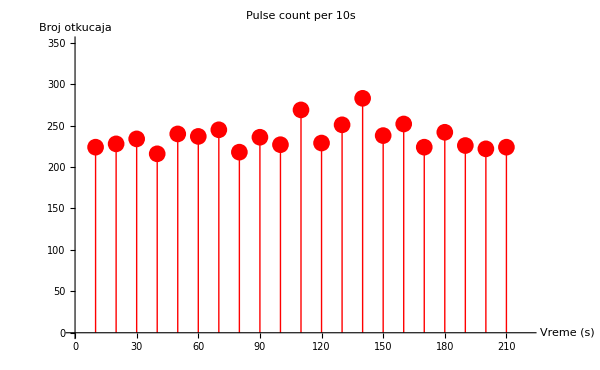

```mathematica
sviPodaci2=Import["D:\\Fizika\\FTN Cacak\\RMFP\\2021-22\\14. Nuklearna fizika\\Radioaktivno socivo ABG.xlsx"];
ListPlot[{sviPodaci2[[1,All,{1,2}]]},
PlotStyle->{Red,PointSize[0.020]},
Filling->Axis,
FillingStyle->Red,
PlotLabel->Style["Pulse count per 10s",Black,Italic],
PlotRange->{{0,220},{0,350}},
AxesLabel->{"Vreme (s)","Broj otkucaja"},

AxesOrigin->{0,0},
ImageSize->{600,Automatic}]
```

```mathematica
(* OBJASNITI NAREDBE Flatten I First@ *)
```

```mathematica
sviPodaci3=Import["D:\\Fizika\\FTN Cacak\\RMFP\\2021-22\\14. Nuklearna fizika\\Radioaktivno socivo ABG - Copy.xlsx"]//Transpose
```

{{{10.,224.}},{{20.,228.}},{{30.,234.}},{{40.,216.}},{{50.,240.}},{{60.,237.}},{{70.,245.}},{{80.,218.}},{{90.,236.}},{{100.,227.}},{{110.,269.}},{{120.,229.}},{{130.,251.}},{{140.,283.}},{{150.,238.}},{{160.,252.}},{{170.,224.}},{{180.,242.}},{{190.,226.}},{{200.,222.}},{{210.,224.}}}

```mathematica
MatrixForm[sviPodaci3]
```

((10.
224.)
(20.
228.)
(30.
234.)
(40.
216.)
(50.
240.)
(60.
237.)
(70.
245.)
(80.
218.)
(90.
236.)
(100.
227.)
(110.
269.)
(120.
229.)
(130.
251.)
(140.
283.)
(150.
238.)
(160.
252.)
(170.
224.)
(180.
242.)
(190.
226.)
(200.
222.)
(210.
224.))

```mathematica
(* OVAKO GORE NAPISANA MATRICA NE VALJA *)
```

```mathematica
sviPodaci3=Import["D:\\Fizika\\FTN Cacak\\RMFP\\2021-22\\14. Nuklearna fizika\\Radioaktivno socivo ABG - Copy.xlsx"]//Transpose
```

{{{10.,224.}},{{20.,228.}},{{30.,234.}},{{40.,216.}},{{50.,240.}},{{60.,237.}},{{70.,245.}},{{80.,218.}},{{90.,236.}},{{100.,227.}},{{110.,269.}},{{120.,229.}},{{130.,251.}},{{140.,283.}},{{150.,238.}},{{160.,252.}},{{170.,224.}},{{180.,242.}},{{190.,226.}},{{200.,222.}},{{210.,224.}}}

```mathematica
MatrixForm[Flatten[sviPodaci3,1]]
```

(10. | 224.
20. | 228.
30. | 234.
40. | 216.
50. | 240.
60. | 237.
70. | 245.
80. | 218.
90. | 236.
100. | 227.
110. | 269.
120. | 229.
130. | 251.
140. | 283.
150. | 238.
160. | 252.
170. | 224.
180. | 242.
190. | 226.
200. | 222.
210. | 224.)

```mathematica
(* OVAKO GORE NAPISANA MATRICA JE U REDU. ILI MOŽE DA SE KORISTI NAREDBA First@ KAO ŠTO JE POKAZANO DOLE *)
```

```mathematica
sviPodaci3=First@Import["D:\\Fizika\\FTN Cacak\\RMFP\\2021-22\\14. Nuklearna fizika\\Radioaktivno socivo ABG - Copy.xlsx"]
```

{{10.,224.},{20.,228.},{30.,234.},{40.,216.},{50.,240.},{60.,237.},{70.,245.},{80.,218.},{90.,236.},{100.,227.},{110.,269.},{120.,229.},{130.,251.},{140.,283.},{150.,238.},{160.,252.},{170.,224.},{180.,242.},{190.,226.},{200.,222.},{210.,224.}}

```mathematica
MatrixForm[sviPodaci3]
```

(10. | 224.
20. | 228.
30. | 234.
40. | 216.
50. | 240.
60. | 237.
70. | 245.
80. | 218.
90. | 236.
100. | 227.
110. | 269.
120. | 229.
130. | 251.
140. | 283.
150. | 238.
160. | 252.
170. | 224.
180. | 242.
190. | 226.
200. | 222.
210. | 224.)

{a_1→0.0314286,a_2→232.971}

0.0314286

232.971

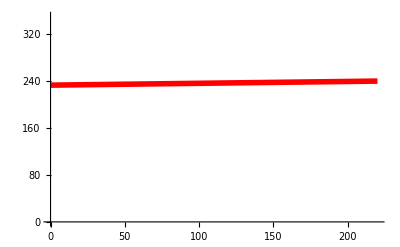

```mathematica
ClearAll["Global`*"]
sviPodaci3=First@Import["D:\\Fizika\\FTN Cacak\\RMFP\\2021-22\\14. Nuklearna fizika\\Radioaktivno socivo ABG.xlsx"];
resenja=FindFit[sviPodaci3,Subscript[a, 1]*x+Subscript[a, 2],{Subscript[a, 1],Subscript[a, 2]},x]
Subscript[b, 1]=Subscript[a, 1]/.resenja[[1]]
Subscript[b, 2]=Subscript[a, 2]/.resenja[[2]]
Plot[Subscript[b, 1]*x+Subscript[b, 2],{x,0,220},PlotStyle->{Red,Thickness[0.01]},PlotRange->{{0,220},{0,350}}]
```

```mathematica
ClearAll["Global`*"]
sviPodaci4=Import["D:\\Fizika\\FTN Cacak\\RMFP\\2021-22\\14. Nuklearna fizika\\Radioaktivno socivo ABG.xlsx"];
resenja1=FindFit[Flatten[sviPodaci4,1],Subscript[c, 1]*x+Subscript[c, 2],{Subscript[c, 1],Subscript[c, 2]},x]
Subscript[d, 1]=Subscript[c, 1]/.resenja1[[1]]
Subscript[d, 2]=Subscript[c, 2]/.resenja1[[2]]
Plot[Subscript[d, 1]*x+Subscript[d, 2],{x,0,220},PlotStyle->{Red,Thickness[0.01]},PlotRange->{{0,220},{0,350}}]
```

{c_1→0.0314286,c_2→232.971}

0.0314286

232.971

-Graphics-

```mathematica
Lančana reakcija U 235
```

```mathematica
u={{Lighter[Blue,0.7],EdgeForm[Black],Disk[{0,0},1]},
{Text[Style["U-235",Bold,12],{0,0}]}};
ba={{Lighter[Orange,0.7],EdgeForm[Black],Disk[{0,0},0.8]},
{Text[Style["Ba-141",Bold,9],{0,0}]}};
kr={{Lighter[Green,0.5],EdgeForm[Black],Disk[{0,0},0.8]},
{Text[Style["Kr-92",Bold,9],{0,0}]}};
n={{Lighter[Red,0.7],EdgeForm[Black],Disk[{0,0},0.5]},
{Text[Style["n",Bold,12],{0,0}]}};
energy={
{White,Disk[{2.1,0},0.7]},
{White,Disk[{2.1*(Sqrt[2]/2),(Sqrt[2])},0.7]},
{White,Disk[{0,2.1},0.8]},
{White,Disk[{-2.1*(Sqrt[2]/2),(Sqrt[2])},0.7]},
{White,Disk[{-2.1,0},0.7]},
{White,Disk[{-2.1*(Sqrt[2]/2),-(Sqrt[2])},0.7]},
{White,Disk[{0,-2.1},0.8]},
{White,Disk[{2.1*(Sqrt[2]/2),-(Sqrt[2])},0.7]},
{Yellow,EdgeForm[Black],Disk[{0,0},2]},
{Text[Style["Energija",Bold,9],{0,0}]}
};
Manipulate[
Show[
Graphics[{
Translate[{{EdgeForm[Thin],White,Rectangle[{-10,10},{10,4}]},
{Text[If[t≤-8,Style["1",Blue,Bold,14],Style["1",14]],{-8,9}]},
{Text[If[-8<t≤-4,Style["2",Blue,Bold,14],Style["2",14]],{-4,9}]},
{Text[If[-4<t≤0,Style["3",Blue,Bold,14],Style["3",14]],{0,9}]},
{Text[If[0<t≤4,Style["4",Blue,Bold,14],Style["4",14]],{4,9}]},
{Text[If[4<t,Style["5",Blue,Bold,14],Style["5",14]],{8,9}]},
{If[-8≥ t,Text[Pane[Style["Slobodni neutron se sudara sa jezgrom U 235. Ovo se može desiti spontano ili u nuklearnim reaktorima ili kada eksplodira atomska bomba. ",TextAlignment->Left,16],400],{1.5,6.4}],{}]},
{If[-8<t≤-4,Text[Pane[Style["Kada se neutron sudari sa jezgrom, jezgro postaje veoma nestabilno.",TextAlignment->Left,16],400],{1.5,6.8}],{}]},
{If[-4<t≤0,Text[Pane[Style["Jezgro se potom cepa na dva produkta - fisiona fragmenta i emituje se nekoliko neutrona. Takođe, oslobađa se velika količina energije.",TextAlignment->Left,16],399],{1.5,6.8}],{}]},
{If[0<t≤4,Text[Pane[Style["Ukoliko postoji kritična masa (dovoljna za lančanu reakciju), neutroni će nastaviti da se sudaraju sa jezgrima.",TextAlignment->Left,16],400],{1.5,6.8}],{}]},
{If[4<t,Text[Pane[Style["Lančana reakcija se nastavlja i oslobađa se još neutrona.",TextAlignment->Left,16],400],{1.5,7.2}],{}]}},{0,-3}],
{If[t≤-8,Translate[n,{t,-4.5}],Translate[n,{-8,-4.5}]]},
{If[-3<t≤-1,{Red,Arrow[{{-8,-4.4},{-7+((t+3)*(4/3)),-4.4+((t+3)*1.2)}}]},{}]},
{If[-1<t,{Red,Arrow[{{-8,-4.4},{-4,-2}}]},{}]},
{If[-3<t≤-1,{Red,Arrow[{{-8,-4.6},{-7+((t+3)*(4/3)),-4.6-((t+3)*1.2)}}]},{}]},
{If[-1<t,{Red,Arrow[{{-8,-4.6},{-4,-7}}]},{}]},
{If[-1<t,Translate[Scale[energy,0.5],{-3,-4.5}],{}]},
{If[-4<t≤-1,Translate[Scale[energy,0.5],{-8+((5/3)*(t+4)),-4.5}],{}]},
{If[-4<t≤2,Translate[n,{-8+((t+4)*(10/6)),-4.5+((t+4)*(3.5/6))}],{}]},
{If[-4<t≤2,Translate[n,{-8+((t+4)*(10/6)),-4.5}],{}]},
{If[-4<t≤2,Translate[n,{-8+((t+4)*(10/6)),-4.5-((t+4)*(3.5/6))}],{}]},
{If[-1<t,Translate[ba,{-3,-2}]],{}},
{If[-1<t,Translate[kr,{-3,-7}]],{}},
{If[-4<t≤-1,Translate[ba,{-8+((5/3)*(t+4)),-4.5+((2.5/3)*(t+4))}]],{}},
{If[-4<t≤-1,Translate[kr,{-8+((5/3)*(t+4)),-4.5-((2.5/3)*(t+4))}]],{}},
{If[5<t≤7,{Red,Arrow[{{2,-4.4},{3+((t-5)*(4/3)),-4.4+((t-5)*(1.4/2))}}]},{}]},
{If[7<t,{Red,Arrow[{{2,-4.4},{6,-3}}]},{}]},
{If[5<t≤7,{Red,Arrow[{{2,-4.6},{3+((t-5)*(4/3)),-4.6-((t-5)*(1.4/2))}}]},{}]},
{If[7<t,{Red,Arrow[{{2,-4.6},{6,-6}}]},{}]},
{If[7<t,Translate[Scale[energy,0.4],{7,-4.5}],{}]},
{If[4<t≤7,Translate[Scale[energy,0.4],{2+((5/3)*(t-4)),-4.5}],{}]},
{If[4<t≤8,Translate[Scale[n,0.5],{2+((t-4)*(10/6)),-4.5+((t-4)*(1.8/6))}],{}]},
{If[4<t≤8,Translate[Scale[n,0.5],{2+((t-4)*(10/6)),-4.5}],{}]},
{If[4<t≤8,Translate[Scale[n,0.5],{2+((t-4)*(10/6)),-4.5-((t-4)*(1.8/6))}],{}]},
{If[8<t,Translate[Scale[n,0.5],{2+((8-4)*(10/6)),-4.5+((8-4)*(1.8/6))}],{}]},
{If[8<t,Translate[Scale[n,0.5],{2+((8-4)*(10/6)),-4.5}],{}]},
{If[8<t,Translate[Scale[n,0.5],{2+((8-4)*(10/6)),-4.5-((8-4)*(1.8/6))}],{}]},
{If[7<t,Translate[Scale[ba,0.5],{7,-4.5+((1.2/3)*(7-4))}]],{}},
{If[7<t,Translate[Scale[kr,0.5],{7,-4.5-((1.2/3)*(7-4))}]],{}},
{If[4<t≤7,Translate[Scale[ba,0.5],{2+((5/3)*(t-4)),-4.5+((1.2/3)*(t-4))}]],{}},
{If[4<t≤7,Translate[Scale[kr,0.5],{2+((5/3)*(t-4)),-4.5-((1.2/3)*(t-4))}]],{}},
{If[5<t≤7,{Red,Arrow[{{2,3.5-4.4},{3+((t-5)*(4/3)),3.5-4.4+((t-5)*(1.2/2))}}]},{}]},
{If[7<t,{Red,Arrow[{{2,3.5-4.4},{6,3.5-4.4+((7-5)*(1.2/2))}}]},{}]},
{If[5<t≤7,{Red,Arrow[{{2,3.5-4.6},{3+((t-5)*(4/3)),3.5-4.6-((t-5)*(1.2/2))}}]},{}]},
{If[7<t,{Red,Arrow[{{2,3.5-4.6},{6,3.5-4.4-((7-5)*(1.2/2))}}]},{}]},
{If[7<t,Translate[Scale[energy,0.4],{7,3.5-4.5}],{}]},
{If[4<t≤7,Translate[Scale[energy,0.4],{2+((5/3)*(t-4)),3.5-4.5}],{}]},
{If[4<t≤8,Translate[Scale[n,0.5],{2+((t-4)*(10/6)),3.5-4.5+((t-4)*(1.8/6))}],{}]},
{If[4<t≤8,Translate[Scale[n,0.5],{2+((t-4)*(10/6)),3.5-4.5}],{}]},
{If[4<t≤8,Translate[Scale[n,0.5],{2+((t-4)*(10/6)),3.5-4.5-((t-4)*(1.8/6))}],{}]},
{If[8<t,Translate[Scale[n,0.5],{2+((8-4)*(10/6)),3.5-4.5+((8-4)*(1.8/6))}],{}]},
{If[8<t,Translate[Scale[n,0.5],{2+((8-4)*(10/6)),3.5-4.5}],{}]},
{If[8<t,Translate[Scale[n,0.5],{2+((8-4)*(10/6)),3.5-4.5-((8-4)*(1.8/6))}],{}]},
{If[7<t,Translate[Scale[ba,0.5],{7,3.5-4.5+((1.2/3)*(7-4))}]],{}},
{If[7<t,Translate[Scale[kr,0.5],{7,3.5-4.5-((1.2/3)*(7-4))}]],{}},
{If[4<t≤7,Translate[Scale[ba,0.5],{2+((5/3)*(t-4)),3.5-4.5+((1.2/3)*(t-4))}]],{}},
{If[4<t≤7,Translate[Scale[kr,0.5],{2+((5/3)*(t-4)),3.5-4.5-((1.2/3)*(t-4))}]],{}},
{If[5<t≤7,{Red,Arrow[{{2,-3.5-4.4},{3+((t-5)*(4/3)),-3.5-4.4+((t-5)*(1.2/2))}}]},{}]},
{If[7<t,{Red,Arrow[{{2,-3.5-4.4},{6,-3.5-4.4+((7-5)*(1.2/2))}}]},{}]},
{If[5<t≤7,{Red,Arrow[{{2,-3.5-4.6},{3+((t-5)*(4/3)),-3.5-4.6-((t-5)*(1.2/2))}}]},{}]},
{If[7<t,{Red,Arrow[{{2,-3.5-4.6},{6,-3.5-4.4-((7-5)*(1.2/2))}}]},{}]},
{If[7<t,Translate[Scale[energy,0.4],{7,-3.5-4.5}],{}]},
{If[4<t≤7,Translate[Scale[energy,0.4],{2+((5/3)*(t-4)),-3.5-4.5}],{}]},
{If[4<t≤8,Translate[Scale[n,0.5],{2+((t-4)*(10/6)),-3.5-4.5+((t-4)*(1.8/6))}],{}]},
{If[4<t≤8,Translate[Scale[n,0.5],{2+((t-4)*(10/6)),-3.5-4.5}],{}]},
{If[4<t≤8,Translate[Scale[n,0.5],{2+((t-4)*(10/6)),-3.5-4.5-((t-4)*(1.8/6))}],{}]},
{If[8<t,Translate[Scale[n,0.5],{2+((8-4)*(10/6)),-3.5-4.5+((8-4)*(1.8/6))}],{}]},
{If[8<t,Translate[Scale[n,0.5],{2+((8-4)*(10/6)),-3.5-4.5}],{}]},
{If[8<t,Translate[Scale[n,0.5],{2+((8-4)*(10/6)),-3.5-4.5-((8-4)*(1.8/6))}],{}]},
{If[7<t,Translate[Scale[ba,0.5],{7,-3.5-4.5+((1.2/3)*(7-4))}]],{}},
{If[7<t,Translate[Scale[kr,0.5],{7,-3.5-4.5-((1.2/3)*(7-4))}]],{}},
{If[4<t≤7,Translate[Scale[ba,0.5],{2+((5/3)*(t-4)),-3.5-4.5+((1.2/3)*(t-4))}]],{}},
{If[4<t≤7,Translate[Scale[kr,0.5],{2+((5/3)*(t-4)),-3.5-4.5-((1.2/3)*(t-4))}]],{}},
{Translate[u,{-8,-4.5}]},
{Translate[u,{2,-1}]},
{Translate[u,{2,-4.5}]},
{Translate[u,{2,-8}]}
},PlotRange->{{-11,11},{-11,7}}],
ImageSize->1.125{500,420}],
{{t,-10,"fisioni proces"},-10,10,ControlType->Slider,Appearance->"Labeled"},SaveDefinitions->True,ControlPlacement->Top
]
```

```mathematica
Heineken pivo
```

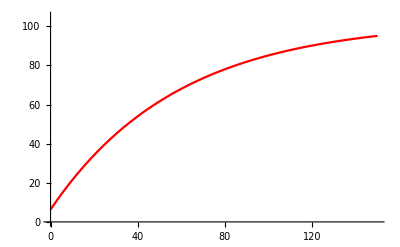

```mathematica
ClearAll["Global`*"]
ClearAll[Evaluate[Context[]<>"*"]]
y0=102.4376;
a1=0.93844;
t1=58.39493;
Plot[y0(1-a1*Exp[-x/t1]),{x,0,150},PlotStyle->Red,PlotRange->{0,105}]
```

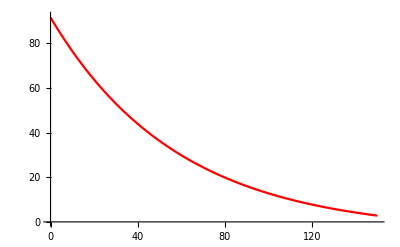

```mathematica
ClearAll["Global`*"]
ClearAll[Evaluate[Context[]<>"*"]]
y0=102.4376;
a1=0.93844;
t1=58.39493;
Plot[-107+y0(1+a1*Exp[-x/t1]),{x,0,150},PlotStyle->Red,PlotRange->{0,92}]
```

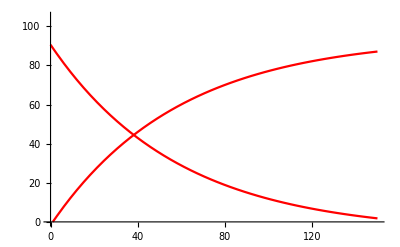

```mathematica
ClearAll["Global`*"]
ClearAll[Evaluate[Context[]<>"*"]]
y0=102.4376;
a1=0.93844;
t1=58.39493;
Plot[{-8+y0(1-a1*Exp[-x/t1]),-108+y0(1+a1*Exp[-x/t1])},{x,0,150},PlotStyle->Red,PlotRange->{0,105}]
```

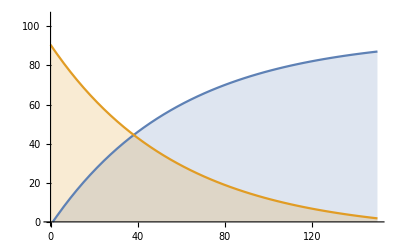

```mathematica
ClearAll["Global`*"]
ClearAll[Evaluate[Context[]<>"*"]]
y0=102.4376;
a1=0.93844;
t1=58.39493;
Plot[{-8+y0(1-a1*Exp[-x/t1]),-108+y0(1+a1*Exp[-x/t1])},{x,0,150},Filling->Axis,PlotRange->{0,105}]
```

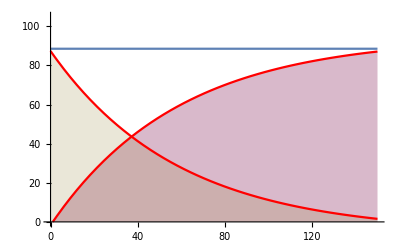

```mathematica
ClearAll["Global`*"]
ClearAll[Evaluate[Context[]<>"*"]]
y0=102.4376;
a1=0.93844;
t1=58.39493;
f1=
Plot[{88.5,-8+y0(1-a1*Exp[-x/t1]),-108+y0(1+a1*Exp[-(x+2)/t1])},{x,0,150},Filling->{{2->Axis},{3->Axis}},PlotRange->{0,105},PlotStyle->{Grey,Red,Red}]
```

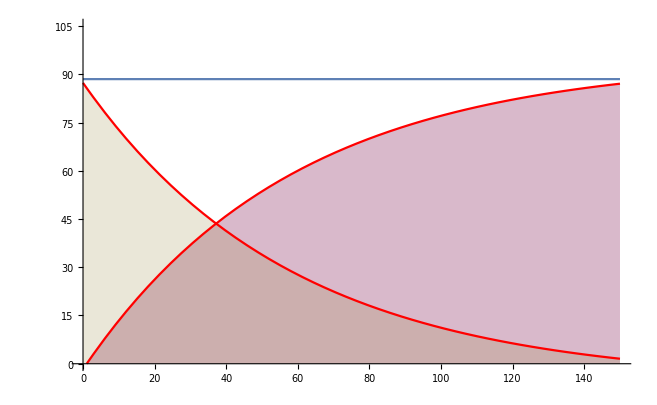
```mathematica
ClearAll["Global`*"]
DynamicModule[{p={{30,30},{50,35},{70,15}}},
{LocatorPane[Dynamic[p],-Graphics-],Dynamic[p]}
]
```

```mathematica
Exponential Decay
```

```mathematica
Manipulate[Plot[Evaluate[{If[u<t,ⅇ^(-a u)],If[u>t,ⅇ^(-a u)]}],{u,0,12.1},Filling->Axis,PlotRange->{{0,12},{0,1}},ImageSize->600,PlotLabel->PaddedForm[Row[{Graphics[{Blue,Disk[{0,0.1},1-ⅇ^(-a t)]},PlotRange->1.5,ImageSize->30,BaselinePosition->(Center->Center)],100 N[1-ⅇ^(-a t)],"% raspadnuta jezgra     ",100 N[ⅇ^(-a t)],"%  preostala jezgra",Graphics[{Red,Disk[{0,0.1},ⅇ^(-a t)]},PlotRange->1.5,ImageSize->30,BaselinePosition->(Center->Center)]}],{3,1}]],
{{t,2,"proteklo vreme t (T_(1/2)) "},0,12,0.02,Appearance->"Labeled"},
{{a,.2,"konstanta radioaktivnog 
         raspada λ ((T_(1/2))^-1)"},0.01,1.5,0.001,Appearance->"Labeled"}]
```

```mathematica
Half-Life of a Radioactive Decay
```

```mathematica
Manipulate[
Grid[{{Show[
Plot[10*Exp[-.00012096*t1],{t1,0,35000},PlotStyle->Dashed,AxesLabel->{"time (years)",Style[ "grams C^14",SingleLetterItalics->False]} ],Plot[10*Exp[-.00012096*t11],{t11,0,HeavisideTheta[34380-t]*(t-34380)+34380},PlotStyle->{Thick,Black}],Plot[10*Exp[-.00012096*t11],{t11,0,HeavisideTheta[28650-t]*(t-28650)+28650},PlotStyle->{Thick,Lighter[Cyan]}],Plot[10*Exp[-.00012096*t11],{t11,0,HeavisideTheta[22920-t]*(t-22920)+22920},PlotStyle->{Thick,Pink}],Plot[10*Exp[-.00012096*t11],{t11,0,HeavisideTheta[17190-t]*(t-17190)+17190},PlotStyle->{Thick,Yellow}],Plot[10*Exp[-.00012096*t11],{t11,0,HeavisideTheta[11460-t]*(t-11460)+11460},PlotStyle->{Thick,Red}],
Plot[10*Exp[-.00012096*t11],{t11,0,HeavisideTheta[5730-t]*(t-5730)+5730},PlotStyle->{Thick,Green}]
,ImageSize->{450,400}],
Graphics3D[{Opacity[.10],Gray,Cylinder[{{-8,0,0},{-8,0,10}},1],Opacity[1],Lighter[Blue],Cylinder[{{-8,0,10*Exp[-.00012096*t]},{-8,0,0}},1],
{Black,
Text[Style[Row[{Subsuperscript["C",6,14]," → ",Subsuperscript["N",7,14]," + ",("e")^("-")}],16],{-6,0,14}],Text[Style[Row[{Subscript[Style["t",Italic],"1/2"]," = 5,730 yrs"}],16],{-6,0,12}],Text[Superscript[Style["C",16],14],{-8,0,-1}],
Text[Superscript[Style["N",16],14],{-4,0,-1}]
},
Opacity[.10],Gray,Cylinder[{{-4,0,0},{-4,0,10}},1],Opacity[1],Lighter[Green],Cylinder[{{-4,0,0},{-4,0,Piecewise[{{(10-(10*Exp[(-1.2096*10^-4*t)])),t≤5730},{5,t>5730}}]}},1],Opacity[1],Lighter[Red],Cylinder[{{-4,0,5},{-4,0,Piecewise[{{5,t<5730},{(10-(10*Exp[(-1.2096*10^-4*t)])),t≤2*5730},{7.5,t>2*5730}}]}},1],Opacity[1],Lighter[Yellow],Cylinder[{{-4,0,7.5},{-4,0,Piecewise[{{7.5,t<2*5730},{(10-(10*Exp[(-1.2096*10^-4*t)])),t≤3*5730},{8.75,t>2*5730}}]}},1],Opacity[1],Lighter[Pink],Cylinder[{{-4,0,8.75},{-4,0,Piecewise[{{8.75,t<3*5730},{(10-(10*Exp[(-1.2096*10^-4*t)])),t≤4*5730},{9.375,t>2*5730}}]}},1],Opacity[1],Lighter[Cyan],Cylinder[{{-4,0,9.375},{-4,0,Piecewise[{{9.375,t<4*5730},{(10-(10*Exp[(-1.2096*10^-4*t)])),t≤5*5730},{9.6875,t>3*5730}}]}},1],Opacity[1],Lighter[Black],Cylinder[{{-4,0,9.6875},{-4,0,Piecewise[{{9.6875,t<5*5730},{(10-(10*Exp[(-1.2096*10^-4*t)])),t≤6*5730},{9.84375,t>3*5730}}]}},1]},ViewPoint->{2,-10,2},Boxed->False,ImageSize->{150,400}]}}],
{{t,0.1,"time"},0.1,35000},ControlPlacement->Top]
```

```mathematica
Radioactive Decay of Five Elements: Time Dependence of Remaining Mass
```

```mathematica
Manipulate[
mult=5;
Module[{hl=Which[element=="ytterbium-169",2.77×10^6,element=="strontium-90",9.08×10^8,element=="holmium-166m",3.78×10^10,element=="carbon-14",1.81×10^11,element=="uranium-238",1.41×10^17]},
Show[
Plot[b(ⅇ^(-Log[2]/hl  n)),{n,.01,5hl },AxesOrigin->{0,0},PlotRange-> {0,1000},AxesLabel->{Style[Row[{"time \n",Style["t",Italic]}], 15],Row[{Style[mass[t], 15]}]},PlotLabel->Row[{"half-life = ",hl,"seconds"}],PlotStyle->Orange],
Plot[b(ⅇ^(-Log[2]/(hl )n)),{n,.01,(hl)*q},AxesOrigin->{0,0},PlotRange-> {0,1000},Filling->Bottom],
PlotLabel->Row[{"At " ,NumberForm[(hl)q,{4,3}]," seconds, the remaining mass is ",NumberForm[ b(ⅇ^(-Log[2]q)),{4,3}],"."}],
ImagePadding->{{35,35},{20,10}},ImageSize->{550,350}
]],
{{q,1,"number of half-lives"},1,5,0.01,Appearance->"Labeled"},
{{b,500,"initial mass"},50,1000,Appearance->"Labeled"},
{{element,"ytterbium-169","element"},{"ytterbium-169","strontium-90","holmium-166m","carbon-14","uranium-238"}}]
```

```mathematica
1. zadatak
```

```mathematica
Subsuperscript[Rn,86,222]
```

Rn_86^222

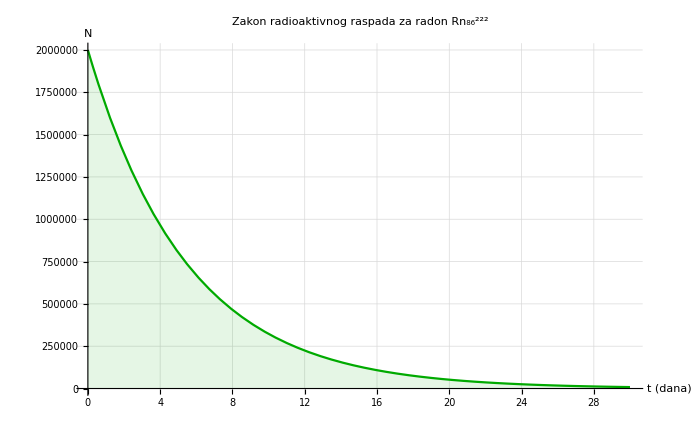

```mathematica
ClearAll["Global`*"];
Subscript[N, 0]=2000000;
Plot[Subscript[N, 0]*Exp[-0.693*x/3.8 ],{x,0,30},PlotStyle->Darker[Green],AxesLabel->{"t (dana)","N"},PlotRange->{{0,30.1},{0,Subscript[N, 0]}},PlotLabel->Style[
"Zakon radioaktivnog raspada za radon Rn_86^222"
,20],LabelStyle->Darker[Blue],GridLines->Automatic, ImageSize->{700,500},Filling->Axis,FillingStyle->Directive[Opacity[0.1],Darker[Green]]]
```

```mathematica
ClearAll["Global`*"]
DynamicModule[{p2={{10,322735},{24,25107}}},
{LocatorPane[Dynamic[p2],
Subscript[N, 0]=2000000;
Plot[
Subscript[N, 0]*Exp[-0.693*x/3.8 ],{x,0,30},PlotStyle->Darker[Green],AxesLabel->{"t (dana)","N"},PlotRange->{{0,30.1},{0,Subscript[N, 0]}},PlotLabel->Style[
"Zakon radioaktivnog raspada za radon Rn_86^222"
,20],LabelStyle->Darker[Blue],GridLines->Automatic, ImageSize->{700,500},Filling->Axis,FillingStyle->Directive[Opacity[0.1],Darker[Green]]
]
],Dynamic[p2]}]
```

```mathematica
2. zadatak
```

```mathematica
Subsuperscript[Po,84,210]
```

Po_84^210

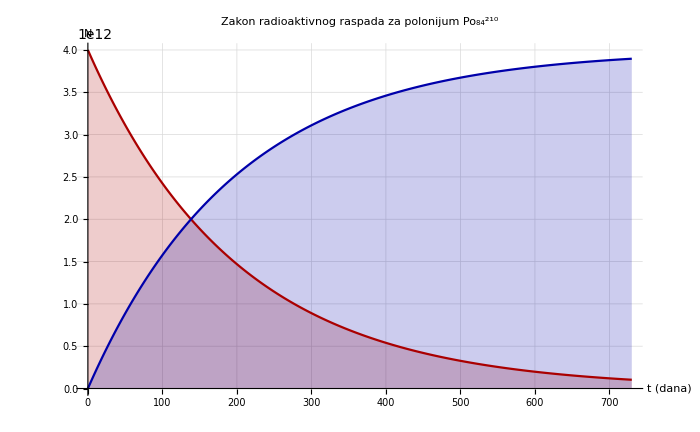

```mathematica
ClearAll["Global`*"];
Subscript[N, 0]=4*^12;
DiscretePlot[{Subscript[N, 0]*Exp[-0.693*x/138.4 ],Subscript[N, 0]-Subscript[N, 0]*Exp[-0.693*x/138.4 ]},{x,0,730},PlotStyle->{Darker[Red],Darker[Blue]},AxesLabel->{"t (dana)","N"},PlotRange->{{0,730},{0,Subscript[N, 0]}},PlotLabel->"
Zakon radioaktivnog raspada za polonijum Po_84^210
",LabelStyle->Darker[Blue],GridLines->Automatic, ImageSize->{700,500}]
```

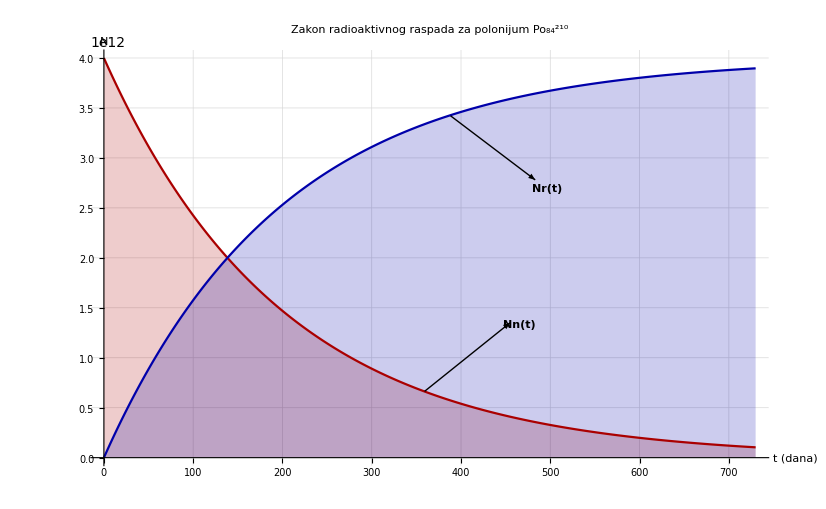

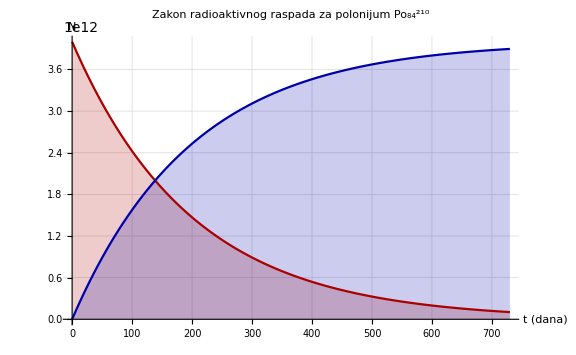
```mathematica
ClearAll["Global`*"]
DynamicModule[{p2={{138.4,2*^12},{365,6.43*^11}}},
{LocatorPane[Dynamic[p2],-Graphics-,LocatorAutoCreate->True],Dynamic[p2]}]
```

```mathematica
3. zadatak
```

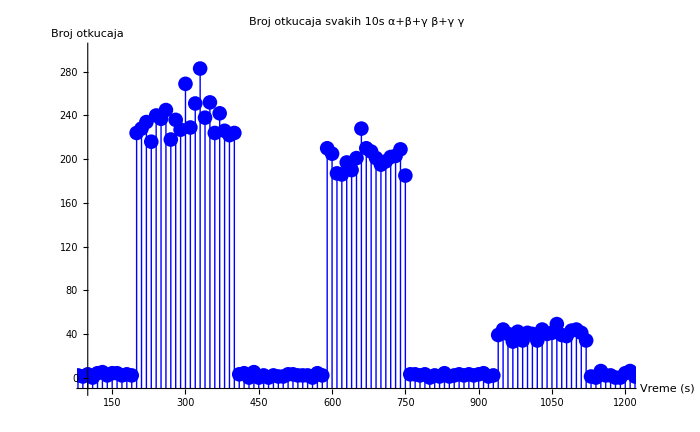

```mathematica
sviPodaci=Import["D:\\Fizika\\FTN Cacak\\RMFP\\2021-22\\14. Nuklearna fizika\\Radioaktivno socivo.xlsx"];
ListPlot[{sviPodaci[[1,All,{1,2}]]},
PlotStyle->{Blue,PointSize[0.015]},
PlotLabel->Style["Broj otkucaja svakih 10s

α+β+γ                                                                                                     
                                                        β+γ                                                 
                                                                                                                       γ",Black,Italic],
Filling->Axis,
FillingStyle->Blue,
PlotRange->{{100,1200},{-10,300}},
AxesLabel->{"Vreme (s)","Broj otkucaja"},
AxesOrigin->{100,-10},
ImageSize->{700,Automatic}]
```

```mathematica
ClearAll["Global`*"]
DynamicModule[{p2={{430,200},{700,230},{1050,100}}}(* proizvolnje kordinate za poziciju lokatora *),
{LocatorPane[Dynamic[p2],-Graphics-,LocatorAutoCreate->True],Dynamic[p2]}]
```

```mathematica
4. zadatak
```

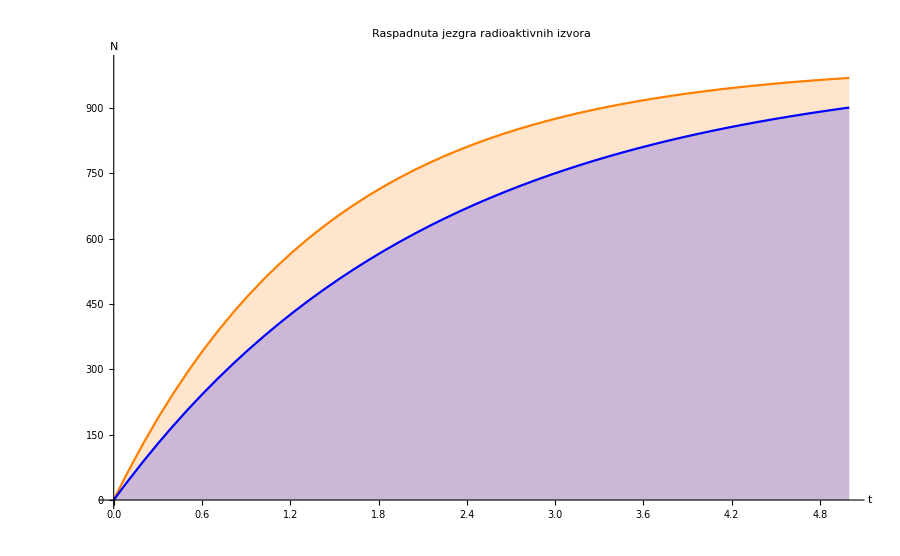

```mathematica
ClearAll["Global`*"];
t1=1;
t2=3/2*t1;
Subscript[N, 0]=1000;
Plot[{Subscript[N, 0]-Subscript[N, 0]*Exp[-0.693*x/t1 ],Subscript[N, 0]-Subscript[N, 0]*Exp[-0.693*x/t2 ]},{x,0,5},PlotStyle->{Orange,Blue},LabelStyle->{Darker[Black],18},Filling->Axis,LabelStyle->{Darker[Black],18},AxesLabel->{"t","N"},PlotRange->{{0,5},{0,Subscript[N, 0]}},PlotLabel->"
Raspadnuta jezgra radioaktivnih izvora
",GridLines->{{{t1,Red},{t2,Blue},{2t1,Red},{2t2,Blue},{3t1,Red},{3t2,Blue},{4t1,Red},{4t2,Blue},{5t1,Red},{5t2,Blue},{6t1,Red},{6t2,Blue},{7t1,Red},{7t2,Blue}},{200,400,600,800,1000}}, ImageSize->{900,700}]
```

```mathematica
ClearAll["Global`*"]
DynamicModule[{p2={{1.294,592},{1.294,450}}},
{LocatorPane[Dynamic[p2],-Graphics-,LocatorAutoCreate->True],Dynamic[p2]}]
```

```mathematica
5. zadatak
```

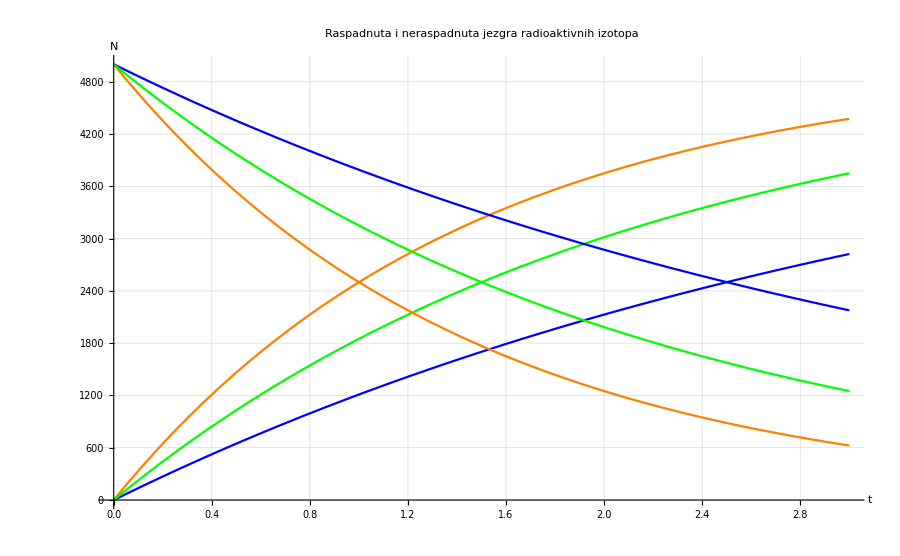

```mathematica
ClearAll["Global`*"];
t1=1;
t2=5/2*t1;
t3=3/2*t1;
Subscript[N, 0]=5000;
Plot[{Subscript[N, 0]-Subscript[N, 0]*Exp[-0.693*x/t1 ],Subscript[N, 0]-Subscript[N, 0]*Exp[-0.693*x/t2 ],Subscript[N, 0]-Subscript[N, 0]*Exp[-0.693*x/t3],Subscript[N, 0]*Exp[-0.693*x/t1],Subscript[N, 0]*Exp[-0.693*x/t2],Subscript[N, 0]*Exp[-0.693*x/t3]},{x,0,3},PlotStyle->{Orange,Blue,Green},LabelStyle->{Darker[Black],18},Filling->None,AxesLabel->{" t","N"},PlotRange->{{0,3},{0,Subscript[N, 0]}},PlotLabel->"
Raspadnuta i neraspadnuta jezgra radioaktivnih izotopa
",LabelStyle->Darker[Black],GridLines->Automatic, ImageSize->{900,650}]
```

```mathematica
ClearAll["Global`*"]
DynamicModule[{p2={{1.106,2675},{1.106,2000},{1.106,1320}}},
{LocatorPane[Dynamic[p2],-Graphics-,LocatorAutoCreate->True],Dynamic[p2]}]
```

```mathematica
6. zadatak
```

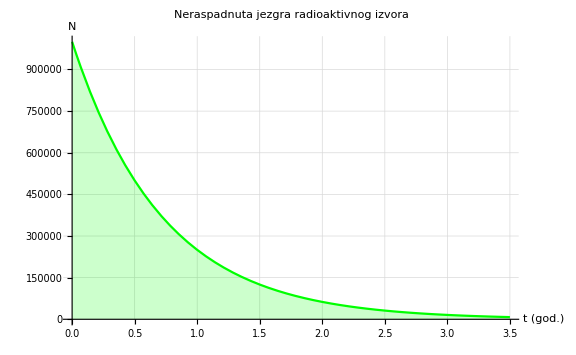

```mathematica
ClearAll["Global`*"];
t1=0.5;
Subscript[N, 0]=1000000;
Plot[{Subscript[N, 0]*Exp[-0.693*x/t1  ]},{x,0,3.5},PlotStyle->{ Green},Filling->Axis,AxesLabel->{"t (god.)","N"},PlotRange->{{0,3.5},{0,Subscript[N, 0]}},PlotLabel->"
Neraspadnuta jezgra radioaktivnog izvora
",LabelStyle->Darker[Black],GridLines->Automatic, ImageSize->Large]
```

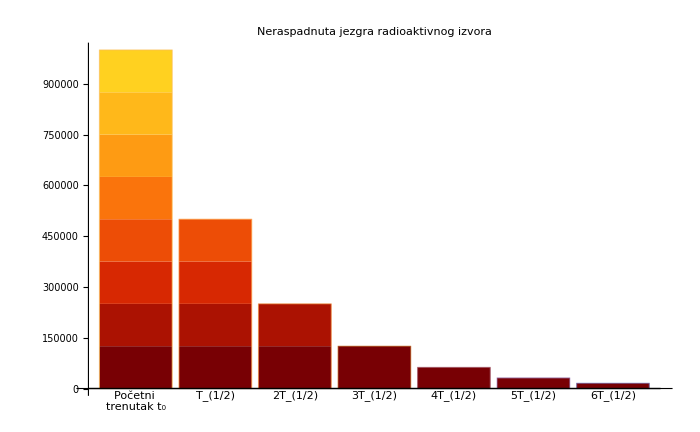

```mathematica
ClearAll["Global`*"];
t1=0.5;
Subscript[N, 0]=1000000;
n=6;
s=8;
k=Table[2^i,{i,0,n}];
BarChart[{Subscript[N, 0]/k},ChartLabels->{"Početni 
trenutak t_0","T_(1/2)","2T_(1/2)","3T_(1/2)","4T_(1/2)","5T_(1/2)","6T_(1/2)"},ChartElementFunction->ChartElementDataFunction["SegmentScaleRectangle","Segments"->s,"ColorScheme"->"SolarColors"],ImageSize->{700,500},LabelStyle->{Black,18},PlotLabel->"
Neraspadnuta jezgra radioaktivnog izvora
"]
```

```mathematica
ClearAll["Global`*"];
t1=0.5;
Subscript[N, 0]=1000000;
n=6;
s=8;
k=Table[2^i,{i,0,n}];
BarChart3D[{Subscript[N, 0]/k},ChartLabels->{"Početni 
trenutak t_0","T_(1/2)","2T_(1/2)","3T_(1/2)","4T_(1/2)","5T_(1/2)","6T_(1/2)"},ImageSize->{700,500},LabelStyle->{Black,18},PlotLabel->"
Neraspadnuta jezgra radioaktivnog izvora
"
]
```

-Graphics3D-

```mathematica
ClearAll["Global`*"]
DynamicModule[{z7={500000}},
{LocatorPane[Dynamic[z7],-Graphics-,LocatorAutoCreate->True],Dynamic[First[z7"jezgara"]]}]
```

```mathematica
ClearAll["Global`*"]
DynamicModule[{p2={500000}},
{LocatorPane[Dynamic[p2],t1=0.5;
Subscript[N, 0]=1000000;
n=6;
s=8;
k=Table[2^i,{i,0,n}];
BarChart[{Subscript[N, 0]/k},ChartElementFunction->ChartElementDataFunction["SegmentScaleRectangle","Segments"->s,"ColorScheme"->"SolarColors"],ImageSize->Large,PlotLabel->"
Neraspadnuta jezgra radioaktivnog izvora
"],LocatorAutoCreate->True],Dynamic[First[p2"jezgara"]]}]
```

```mathematica
8. zadatak
```

```mathematica
ClearAll["Global`*"]
DynamicModule[{zz7={2,16*10^22}},
{LocatorPane[Dynamic[zz7],
t1=0.5;
Subscript[N, 0]=20*10^22;
n=6;
s=20;
k=Table[(2^i-1)/2^i,{i,1,n}];
BarChart[Subscript[N, 0]*k,ChartElementFunction->ChartElementDataFunction["SegmentScaleRectangle","Segments"->s,"ColorScheme"->"SolarColors"], ImageSize->{650,500},PlotLabel->"
Raspadnuta jezgra radioaktivnog izvora
",LabelStyle->{Darker[Black],18},GridLines->Automatic,Epilog->{PointSize[0.03],
Point[Dynamic[{First[zz7],(20*10^22-20*10^22*Exp[-0.693*First[zz7]/1 ])}],
VertexColors->{Black, Opacity[0.8]}]},Background->Gray,ChartLabels->{"T_(1/2)","2T_(1/2)","3T_(1/2)","4T_(1/2)","5T_(1/2)","6T_(1/2)"}],

Appearance->"N_r(t)"],


Dynamic[20*10^22*(1-1*Exp[-Log[2]*First[zz7]/1])"jezgara"]
}]
```

```mathematica
9. zadatak
```

```mathematica
ClearAll["Global`*"]
Subscript[N, 0]=14.2*10^21;
DynamicModule[{z9={30,8.5*10^21}},
{LocatorPane[Dynamic[z9],

Plot[{Subscript[N, 0]-Subscript[N, 0]*Exp[-Log[2]*x/25 ],Subscript[N, 0]*Exp[-Log[2]*x/25 ]},{x,-10,120},PlotStyle->Brown,Filling->Axis,AxesLabel->{"t (min)","N"},PlotRange->{{0,120},{0,15*10^21}},PlotLabel->"
N_r(t) i N_n(t) radioaktivnog izvora Bi_83^212",LabelStyle->{Darker[Black],16},GridLines->Automatic, ImageSize->{900,800},Epilog->{PointSize[0.015],
Point[{
Dynamic[{First[z9],(14.2*10^21-14.2*10^21*Exp[-Log[2]*First[z9]/25 ])}]
},
VertexColors->Red]}],

Appearance->"N_r(t)"],

Dynamic[{First[z9]"min",(14.2*10^21-14.2*10^21*Exp[-Log[2]*First[z9]/25 ])"jezgara"}]
}]
```

```mathematica
10. zadatak
```

```mathematica
Subsuperscript["Ac",89,225]
```

Ac_89^225

```mathematica
ClearAll["Global`*"];
Subscript[N, 0]=17.5*10^21;
DiscretePlot[{8.02*10^(-7)*Subscript[N, 0]*Exp[-0.693*x/10 ]},{x,0,30},PlotStyle->Orange,Filling->Axis,AxesLabel->{"t (dana)","A (Bq)"},PlotRange->{{0,30},{0,16*10^15}},PlotLabel->"
Aktivnost radioaktivnog izvora Ac_89^225
",LabelStyle->{Darker[Black],18},GridLines->Automatic, ImageSize->{800,520}]
```

-Graphics-

```mathematica
ClearAll["Global`*"]
DynamicModule[{z10={{14,9*10^15}}},
{LocatorPane[Dynamic[z10],-Graphics-],Dynamic[z10]}]
```

```mathematica
ClearAll["Global`*"];

Manipulate[
LocatorPane[Dynamic[koordinate],
Show[Subscript[N, 0]=17.5*10^21;
DiscretePlot[{8.02*10^(-7)*Subscript[N, 0]*Exp[-0.693*x/10 ]},{x,0,30},PlotStyle->Black,AxesLabel->{"t (dana)","A (Bq)"},PlotRange->{{0,30},{0,16*10^15}},PlotLabel->"
Aktivnost radioaktivnog izvora Ac_89^225
",LabelStyle->{Darker[Black],18},GridLines->Automatic, ImageSize->{800,520}]
,Epilog->{Red,PointSize[Large],Point[Dynamic[koordinate]]}]
],
{{koordinate,{14,9*10^15}}}]
```

```mathematica
11. zadatak
```

```mathematica
Subsuperscript["I",53,123]
```

I_53^123

```mathematica
ClearAll["Global`*"];
Subscript[N, 0]=4.896*10^22;
DiscretePlot[{Subscript[N, 0]-Subscript[N, 0]*Exp[-0.693*x/13 ],Subscript[N, 0]*Exp[-0.693*x/13 ]},{x,0,96},PlotStyle->Orange,Filling->Axis,AxesLabel->{"t (h)","N"},PlotRange->Automatic,PlotLabel->"
N_r(t) i N_n(t) radioaktivnog izvora I_53^123
",LabelStyle->Darker[Black],GridLines->Automatic, ImageSize->Large]
```

-Graphics-

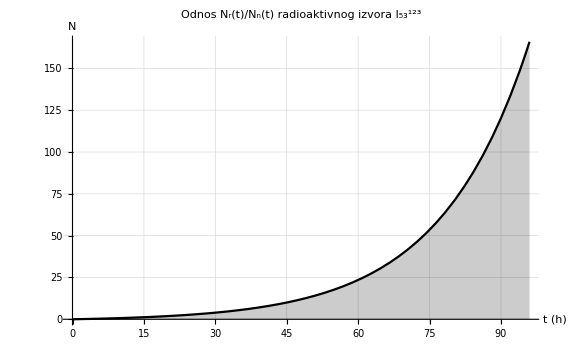

```mathematica
ClearAll["Global`*"];
Subscript[N, 0]=4.896*10^22;
Plot[{(Subscript[N, 0]-Subscript[N, 0]*Exp[-0.693*x/13 ])/(Subscript[N, 0]*Exp[-0.693*x/13 ])},{x,0,96},PlotStyle->Black,Filling->Axis,AxesLabel->{"t (h)","N"},PlotRange->Automatic,PlotLabel->"
Odnos N_r(t)/N_n(t) radioaktivnog izvora I_53^123
",LabelStyle->Darker[Black],GridLines->Automatic, ImageSize->Large]
```

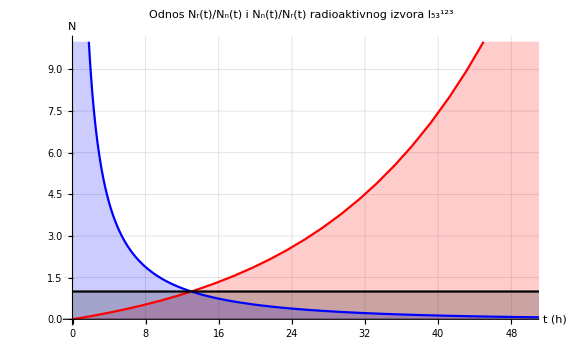

```mathematica
ClearAll["Global`*"];
Subscript[N, 0]=4.896*10^22;
Plot[{(Subscript[N, 0]-Subscript[N, 0]*Exp[-0.693*x/13 ])/(Subscript[N, 0]*Exp[-0.693*x/13 ]),(Subscript[N, 0]*Exp[-0.693*x/13 ])/(Subscript[N, 0]-Subscript[N, 0]*Exp[-0.693*x/13 ]),
((Subscript[N, 0]-Subscript[N, 0]*Exp[-0.693*x/13 ])/(Subscript[N, 0]*Exp[-0.693*x/13 ])*(Subscript[N, 0]*Exp[-0.693*x/13 ])/(Subscript[N, 0]-Subscript[N, 0]*Exp[-0.693*x/13 ]))},{x,0,96},PlotStyle->{Red, Blue,Black},Filling->Axis,AxesLabel->{"t (h)","N"},PlotRange->{{0,50},{0,10}},PlotLabel->"
Odnos N_r(t)/N_n(t) i N_n(t)/N_r(t) radioaktivnog izvora I_53^123
",LabelStyle->Darker[Black],GridLines->Automatic, ImageSize->Large]
```

```mathematica
ClearAll["Global`*"]
DynamicModule[{p2={22,5}},
{LocatorPane[Dynamic[p2],-Graphics-],Dynamic[p2]}]
```

```mathematica
12. zadatak
```

```mathematica
ClearAll["Global`*"];
VisinaPiva=Import["D:\\Fizika\\FTN Cacak\\RMFP\\Praktikum\\Datoteka-Pivo.xlsx"];
plot12=ListPlot[{VisinaPiva[[1,All,{1,2}]]},
PlotStyle->Red,
PlotMarkers->{"◆"},
PlotLabel->Style["
Visina pene Heineken lager piva",Black,Italic],
Filling->Axis,
AxesOrigin->{-10,0},
PlotRange->{{-10,240},{0,140}},
AxesLabel->{"Vreme (s)","h (mm)"},
ImageSize->{850,Automatic}];
Manipulate[LocatorPane[Dynamic[VisinaPiva],Show[plot12,Epilog->{Red,PointSize[Large],Point[Dynamic[VisinaPiva]]}]],{{VisinaPiva,{100,80}}}]
```

Show::gtype: Symbol is not a type of graphics.

{a→118.905,b→0.0297485}

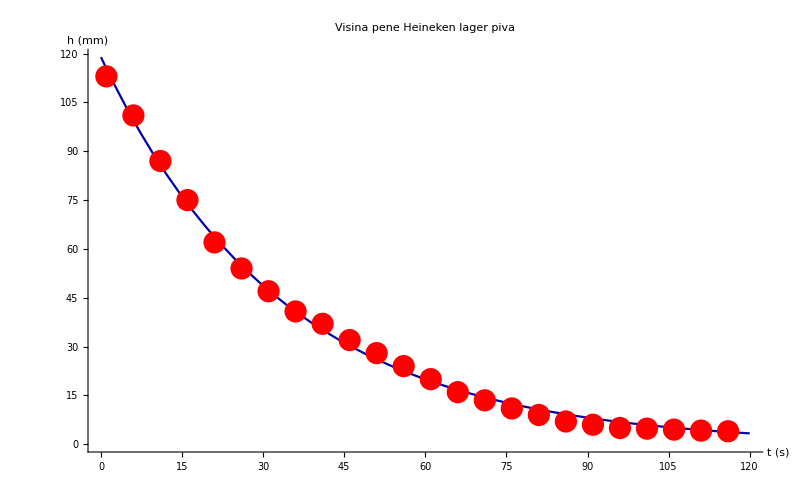

```mathematica
ClearAll["Global`*"];
vreme={1,6,11,16,21,26,31,36,41,46,51,56,61,66,71,76,81,86,91,96,101,106,111,116};
visina={113,101,87,75,62,54,47,40.8,37,32,28,24,20, 16,13.5,11,9,7,6,5,4.8,4.5,4.2,4};
podaci12=Transpose[{vreme,visina}];
MatrixForm[podaci12];
resenje12=FindFit[podaci12,a*E^(-b*x),{a,b},x]
a1=a/.resenje12[[1]];
b1=b/.resenje12[[2]] ;
Show[Plot[a1*E^(-b1*x),{x,0,120},PlotStyle->Darker[Blue],LabelStyle->{Black, 20},PlotLabel->"Visina pene Heineken lager piva",AxesLabel->{"t (s)","h (mm)"}],
        ListPlot[podaci12,PlotStyle->{Red,PointSize[0.02]}],AxesOrigin->Automatic, ImageSize->{800,600}]
```

{a→118.905,b→0.0297485}

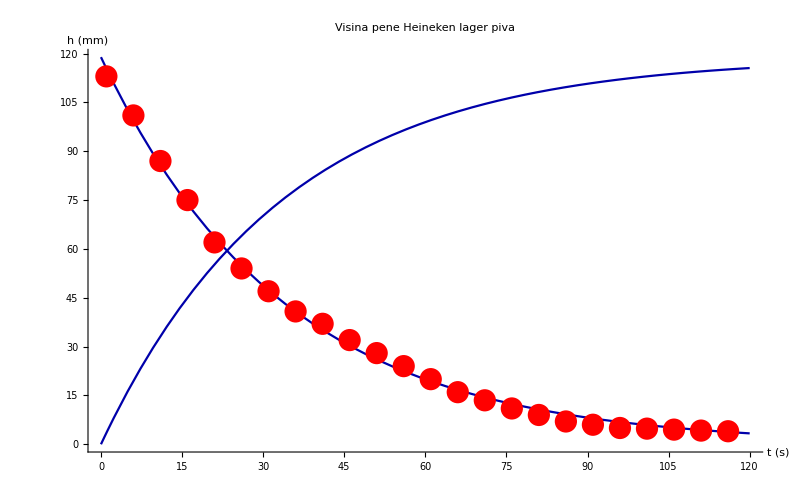

```mathematica
ClearAll["Global`*"];
vreme={1,6,11,16,21,26,31,36,41,46,51,56,61,66,71,76,81,86,91,96,101,106,111,116};
visina={113,101,87,75,62,54,47,40.8,37,32,28,24,20, 16,13.5,11,9,7,6,5,4.8,4.5,4.2,4};
podaci12=Transpose[{vreme,visina}];
MatrixForm[podaci12];
resenje12=FindFit[podaci12,a*E^(-b*x),{a,b},x]
a1=a/.resenje12[[1]];
b1=b/.resenje12[[2]] ;
Show[Plot[{a1*E^(-b1*x),a1*(1-E^(-b1*x))},{x,0,120},PlotStyle->Darker[Blue],LabelStyle->{Black, 20},PlotLabel->"Visina pene Heineken lager piva",AxesLabel->{"t (s)","h (mm)"}],
        ListPlot[podaci12,PlotStyle->{Red,PointSize[0.02]}],AxesOrigin->Automatic, ImageSize->{800,600}]
```

```mathematica
DynamicModule[{p12={23.3,118.9/2}},
{LocatorPane[Dynamic[p12],Plot[{a1*E^(-b1*x),a1*(1-E^(-b1*x))},{x,0,120},PlotStyle->{Darker[Blue],Red},LabelStyle->{Black, 20}, AxesOrigin->Automatic, ImageSize->{800,600},PlotLabel->"Visina pene Heineken lager piva",AxesLabel->{"t (s)","h (mm)"}]
      ],Dynamic[p12]}]
```